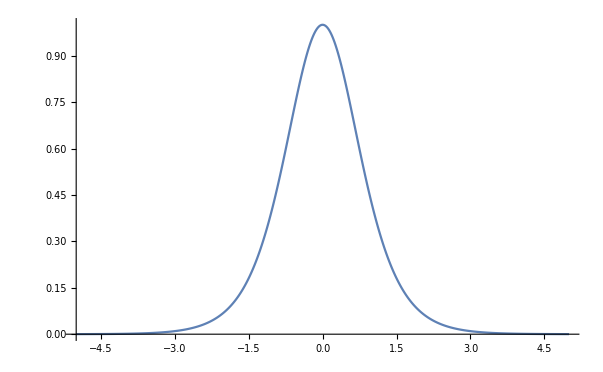

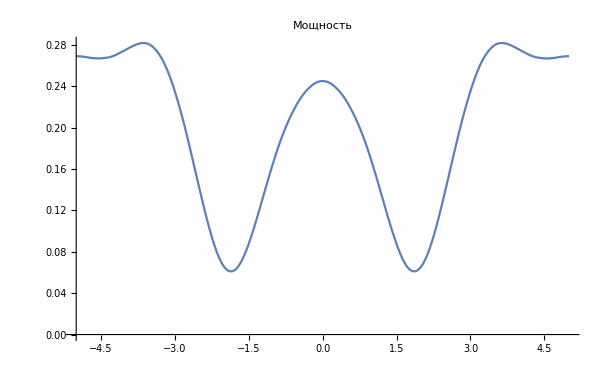

```mathematica
CalcWindow=5;(*ps*)
N0=2047;
h=0.0002;

N0=N0+Boole[EvenQ[N0]];
Sech2Imp[T0_]:=Table[N[Sech[t/T0]],{t,- CalcWindow, CalcWindow,2CalcWindow/(N0-1)}];

β2=-22;γ=1.25;
Imp=Fourier[Sech2Imp[1]];

D2Fourier=Table[-(Pi k/CalcWindow)^2,{k,0,N0/2}]~Join~Table[-(Pi (k-N0)/CalcWindow)^2,{k,Ceiling[N0/2],N0-1}];
FourierOp=Exp[-I β2/2 D2Fourier h];
SpatialOp[x_List]=Exp[I γ Abs[x]^2 h];

ListPlot[(Abs[InverseFourier[Imp]]^2),PlotRange->All,Joined->True,DataRange->{-CalcWindow, CalcWindow},AxesOrigin->{-CalcWindow,0}]

Imp=Sqrt[FourierOp]Imp;
Monitor[
For[ξ=h/2,ξ<1,ξ+=h,

Imp=InverseFourier[Imp];
Imp=Imp SpatialOp[Imp];
Imp=Fourier[Imp];
Imp=FourierOp Imp

],ξ]
Imp=InverseFourier[Imp/Sqrt[FourierOp]];
ListPlot[(Abs[Imp]^2),PlotRange->All,Joined->True,DataRange->{-CalcWindow,CalcWindow},AxesOrigin->{-CalcWindow,0},PlotLabel->"Мощность"]
```

Домашнее задание
1) Сосчитать количество приближений при выводе НУШ из уравнений Максвелла. Объяснить правомерность и смысл каждого из них
2) Доказать, что симметричный вид метода SSFT обладает на порядок более быстрой сходимостью, чем несимметричный.
3) Дана произвольная финитная функция f(t), t∈ℝ. Ее фурье-образ F(ω), ω∈ℝ. Использовать БПФ для нахождения приближенного значения функции F(ω), построить ее график, сравнить с аналитическим F(ω). Оси на графике обозначить в системе SI, считать, что f(t) имеет размерность Sqrt[Вт].
	Преобразование Фурье, Дискретное преобразование Фурье, Ряд Фурье. Из какого пространства в какое выполняются все эти преобразования?
	Есть 2 приближения при использовании БПФ для нахождения фурье образа. Каждое приближение приводит к отклонению найденной функции от фурье образа, первое вызывает blurring, второе aliasing. Объяснить данные эффекты.
	Проверить, что теорема Парсеваля верна
4) Усовершенствовать SSFT алгоритм так, чтобы:
	он включал в себя усиление/ослабление по закону Бугера-Ламберта
	выводилась мгновенная частота
	выводилась плотность мощности спектра излучения после обсчета в координатах (λ, P(λ))
	выводилась фаза спектра излучения. Воспользоваться функцией Arg, далее придумать алгоритм сшивки скачков
	на излучение можно было наложить гауссов спектральный фильтр, действующий в точке (Возможный вариант исполнения: если β2 обладает мнимой частью, то по сути это и будет гаусовский фильтр. Уметь вывести связь Im[β2] и Δλ_FWHM)
5) Пропустить пикосекундный гаусовский импульс через дисперсионный элемент (отлично от нуля только β2), затем через спектральный гауссовский фильтр. Вывести график мощность импульса на входе и выходе системы.
	Вывести формулу для связи спектральной ширины с длительностью гауссова импульса, в случае, когда он накопил GDD (Group Delay Dispersion) = x пс^2
6) Подать на вход волокна γ=0.0058 1/(W m) β2=0.025 ps^2/m g=1.9 1/m (по мощности) гауссов импульс с энергией 12 pJ Tfwhm=1 ps. Вывести импульс, спектр, фазу спектра и мгновенную частоту импульса через 6 м волокна.
	Как убедиться, что в результатах не проявляются артефакты вычислений?
	Прочитать про симиляритоны, показать (устно) что данный импульс обладает всеми признаками симиляритона